```mathematica
maxedges[n_]:=n(n-1)/2
```

```mathematica
generateGraphFormDensity[n_,d_]:=RandomGraph[{n,Round[maxedges[n]*d]}, DirectedEdges->False,  GraphLayout->"CircularEmbedding"] (* GraphLayout->"CircularEmbedding"*)
```

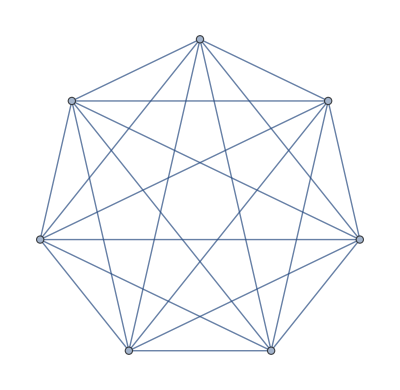

```mathematica
generateGraphFormDensity[7,1]
```

```mathematica
Manipulate[generateGraphFormDensity[Round[n],1],{n,3,40}]
```

```mathematica
Manipulate[generateGraphFormDensity[100,d],{d,0,0.3}]
```

```mathematica
Max[VertexDegree[generateGraphFormDensity[100,0.3]]]
```

40

```mathematica
Table[i,{i,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
data1:=Table[Max[VertexDegree[generateGraphFormDensity[100,0.01]]],{i,0,5000}]
data2:=Table[Max[VertexDegree[generateGraphFormDensity[100,0.05]]],{i,0,5000}]
data3:=Table[Max[VertexDegree[generateGraphFormDensity[100,0.1]]],{i,0,5000}]
data4:=Table[Max[VertexDegree[generateGraphFormDensity[100,0.3]]],{i,0,5000}]
data5:=Table[Max[VertexDegree[generateGraphFormDensity[100,0.8]]],{i,0,5000}]
```

```mathematica
SortBy[Tally[data2], Last][[-1]][[1]] (*gives the most frequent*)
```

11

```mathematica
SortBy[Tally[data], First][[-1]][[1]](*gives the highest*)
```

16

### Function that gives max degree found over a sample of N graph, n nodes, d density

```mathematica
giveMaxDegree[n_,d_,N_]:= SortBy[Tally[Table[Max[VertexDegree[generateGraphFormDensity[n,d]]],{i,0,N}]], First][[-1]][[1]]
```

```mathematica
giveMaxDegree[100,0.1,500]
```

24

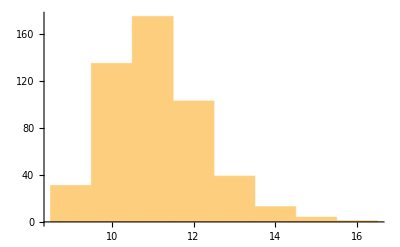

```mathematica
Histogram[data]
```

```mathematica
FindDistribution[data,3]
```

{DataDistribution[…],DataDistribution[…],PascalDistribution[9,0.80177]}

```mathematica
data
```

{10,13,10,12,13,9,10,12,11,12,10,11,13,12,10,10,11,12,11,12,10,13,10,13,11,10,10,11,10,16,10,12,12,10,12,13,9,11,11,10,12,11,11,11,14,10,13,13,10,11,11,10,10,13,12,12,11,10,11,10,11,11,13,10,11,12,11,12,10,10,9,11,10,11,12,10,12,12,10,12,13,11,11,11,10,13,11,11,12,10,10,13,11,13,10,10,13,12,11,12,13,10,11,11,12,12,10,10,11,11,11,11,10,12,11,10,14,12,11,12,11,11,11,12,10,11,11,11,13,10,12,12,11,12,12,9,13,10,14,12,10,10,11,11,11,12,11,13,10,13,12,12,12,11,11,11,11,12,11,10,13,10,11,11,11,11,11,12,12,10,10,11,10,11,11,10,12,12,12,9,12,11,11,11,10,11,11,11,12,11,9,10,12,11,11,11,12,11,11,11,13,13,15,10,11,11,11,12,12,11,14,11,11,11,14,11,10,11,12,11,13,10,11,11,11,11,11,11,12,11,13,12,11,9,9,13,12,10,13,11,11,10,11,10,10,12,12,12,11,10,10,11,9,12,12,11,12,10,10,12,12,14,11,11,11,11,10,11,11,11,12,10,11,11,12,11,10,12,14,11,9,10,10,10,11,10,10,12,12,11,11,12,12,12,10,11,11,12,11,11,11,11,9,11,10,10,11,12,11,11,10,13,12,9,11,11,11,14,10,11,12,11,11,11,11,10,11,12,11,11,11,10,12,10,12,11,13,10,10,12,10,14,11,10,11,12,11,10,12,11,12,11,13,14,10,13,10,11,10,11,11,10,10,13,10,11,9,11,10,12,11,11,11,11,11,14,12,12,13,12,11,10,13,9,10,10,12,10,10,14,10,12,12,11,10,11,12,11,10,12,10,11,11,11,11,9,13,11,9,10,12,10,11,10,10,12,11,10,13,11,10,12,12,12,10,11,11,12,10,11,11,12,10,12,10,11,11,11,10,9,12,12,9,11,13,10,11,10,13,11,15,12,11,10,10,10,12,10,12,10,11,11,12,10,11,12,9,13,10,11,11,13,9,10,12,12,12,11,12,11,12,10,11,10,11,11,9,10,12,15,10,10,11,12,10,11,10,12,11,11,14}

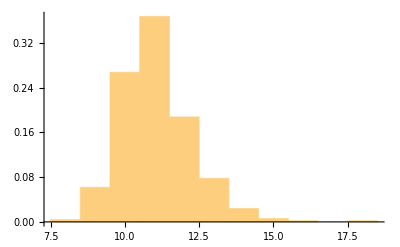

```mathematica
Histogram[%60,20,"ProbabilityDensity"]
```

```mathematica
FindDistributionParameters[data,BinomialDistribution[μ,σ]]
```

{μ→15,σ→0.738789}

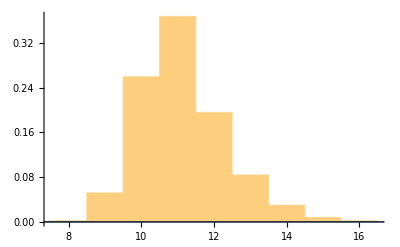

```mathematica
Show[Histogram[data,20,"ProbabilityDensity"],Plot[PDF[BinomialDistribution[10,0.8],x],{x,0,20},PlotStyle->Thick]]
```

RayleighDistribution[3.02611]

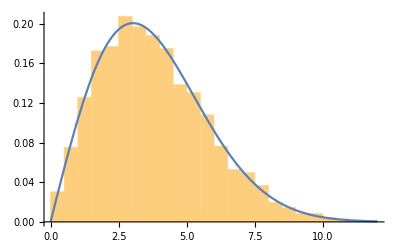

```mathematica
SampleData=RandomVariate[RayleighDistribution[3],5000];
fitDist=EstimatedDistribution[SampleData,RayleighDistribution[s]]
Show[Histogram[SampleData,Automatic,"PDF"],Plot[PDF[fitDist,x],{x,0,12}]]
```

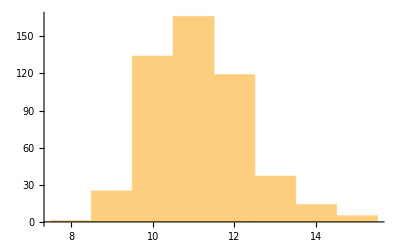

```mathematica
Histogram[data]
```

```mathematica
Tally[data]
```

{{10,126},{13,40},{12,111},{9,21},{11,186},{16,1},{14,13},{15,3}}

```mathematica
SortBy[Tally[data], First][[-1]][[1]]
```

16